```mathematica
Table[Mod[2^(2 3^n)-1,3^(n+1)],{n,30}]
```

$Aborted

```mathematica
Simplify[2^(2 3^n)-1/3^(n+1)]
```

-3^(-1-n)+4^(3^n)

```mathematica
Table[Take[IntegerDigits[2^(2 3^n)-1,3^(n+1)],-3],{n,10}]
```

Take::take: Cannot take positions -3 through -1 in {7,0}.

{Take[{7,0},-3],{8,16,0},{55,16,0},{139,178,0},{671,664,0},{1470,664,0},{440,2851,0},{4957,2851,0},{42912,42217,0},{59938,101266,0}}

```mathematica
Table[Mod[(2^(2 3^n)-1)/(3^(n+1)),3],{n,20}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
2^(2 3^n)-1/.n->20
```

$Aborted[]

```mathematica
SafeTake[l_,n_]:=Take[If[Length[l]<Abs[n],PadLeft[l,Abs[n]],l],n]
```

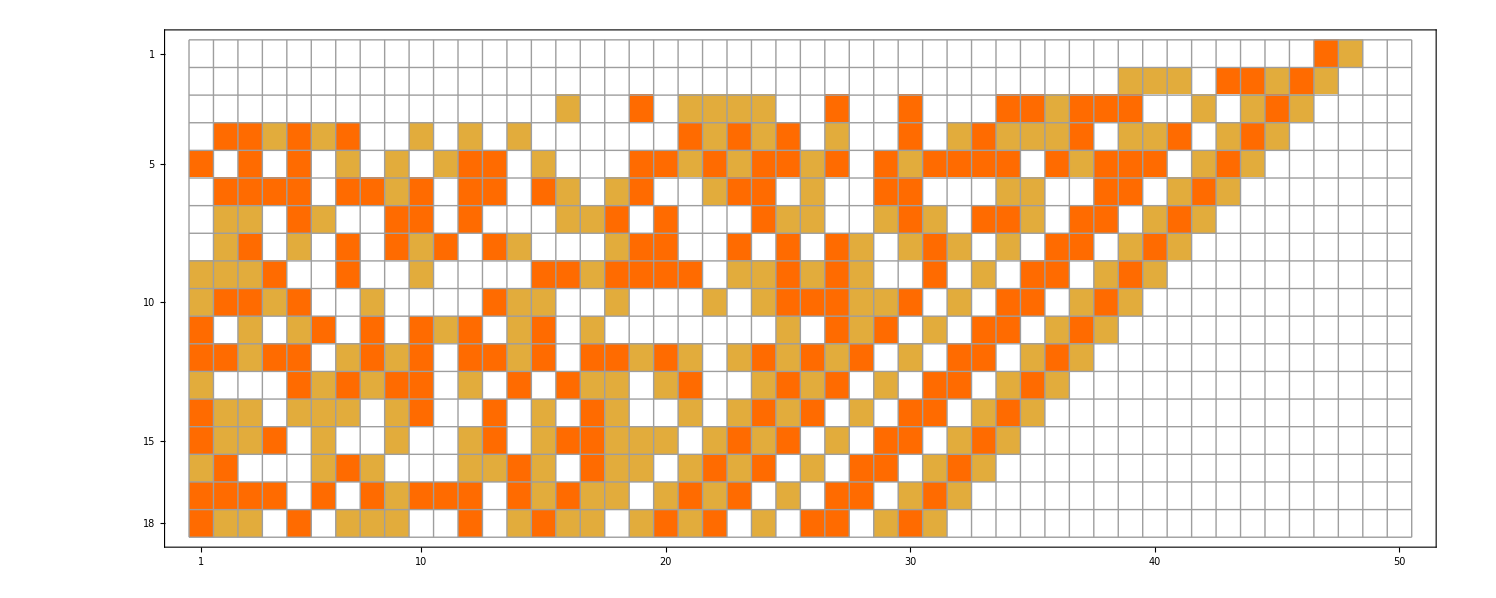

```mathematica
MatrixPlot[Table[SafeTake[IntegerDigits[2^(2 3^n)-1,3],-50],{n,18}],Mesh->True]
```

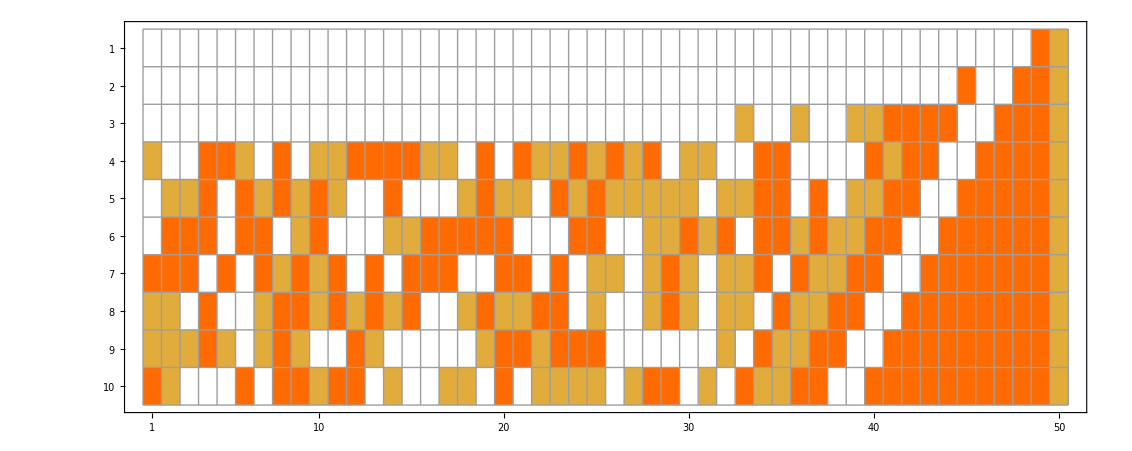

```mathematica
MatrixPlot[Table[SafeTake[IntegerDigits[2^(3^n)-1,3],-50],{n,10}],Mesh->True]
```

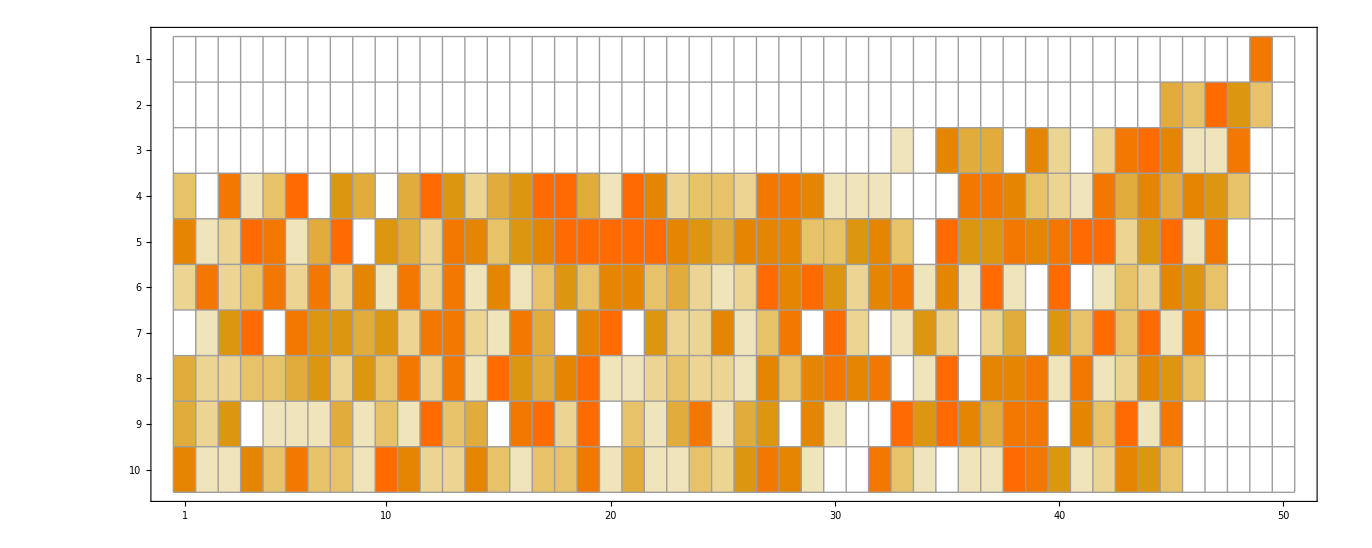

```mathematica
MatrixPlot[Table[SafeTake[IntegerDigits[2^(2 3^n)-1,9],-50],{n,10}],Mesh->True]
```

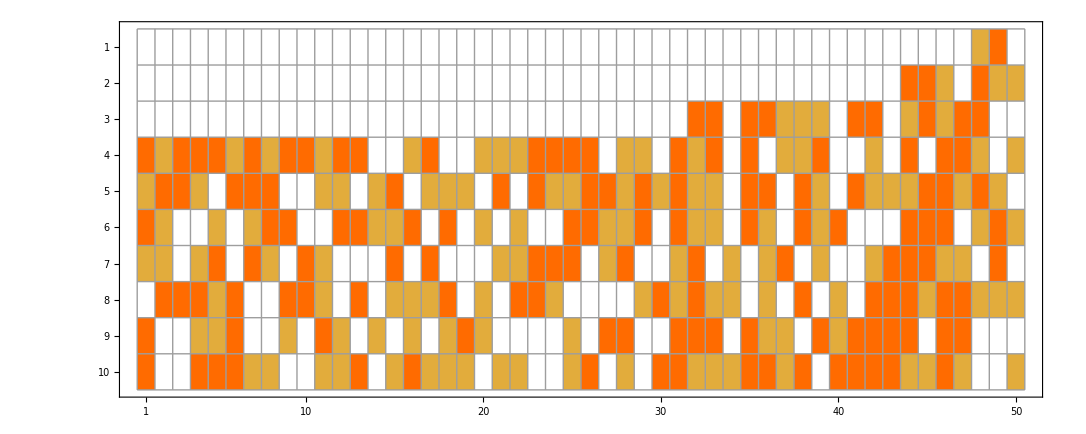

```mathematica
MatrixPlot[Table[SafeTake[IntegerDigits[2^(n+3^n)-1,3],-50],{n,10}],Mesh->True]
```

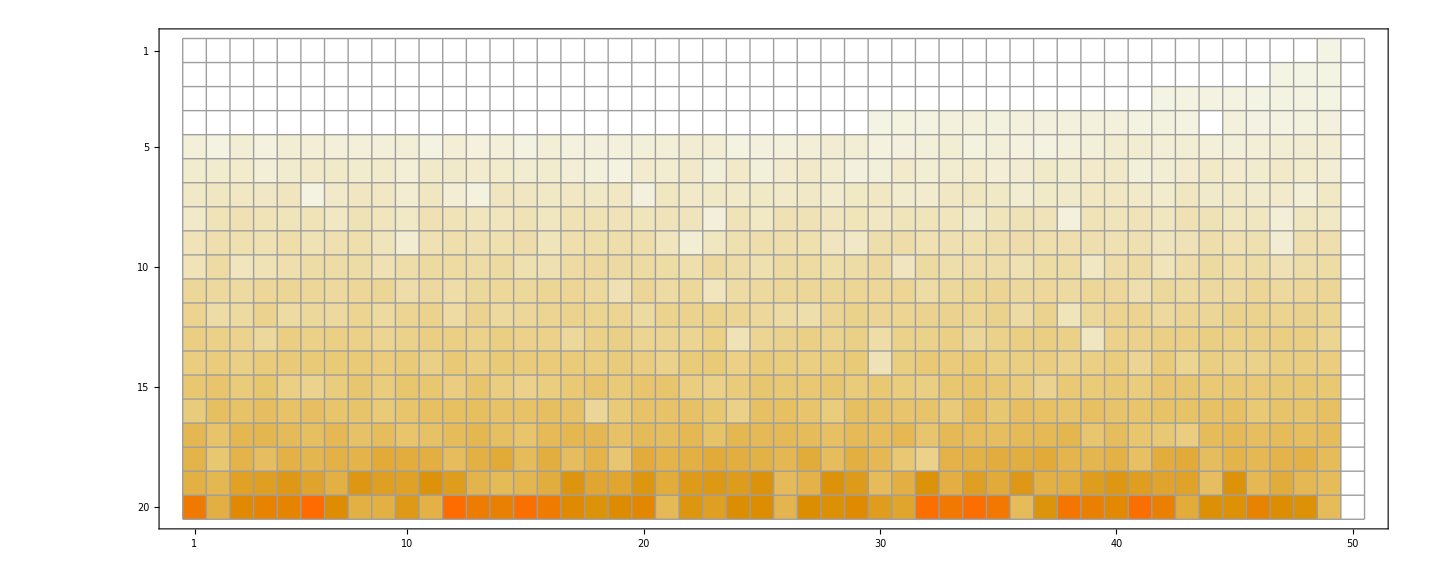

```mathematica
MatrixPlot[Table[SafeTake[IntegerDigits[2^(2 3^n)-1,3^(n+1)],-50],{n,20}],Mesh->True]
```

```mathematica
2^(2 3^n)-1/.n->n-1
```

-1+2^(2 3^(-1+n))

```mathematica
(2^(2 3^n)-1)/(-1+2^(2 3^(-1+n)))//Simplify
```

1+4^(3^(-1+n))+16^(3^(-1+n))

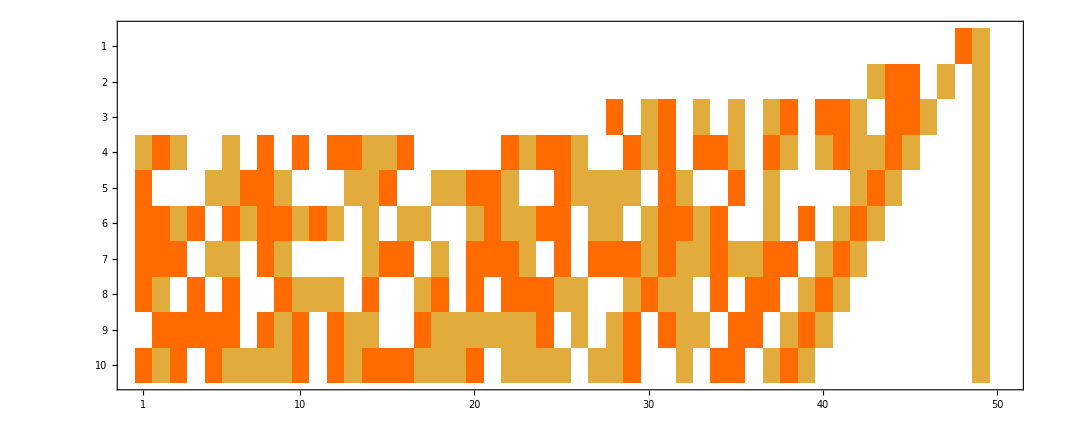

```mathematica
Table[SafeTake[IntegerDigits[1+4^3^(-1+n)+16^3^(-1+n),3],-50],{n,10}]//MatrixPlot
```

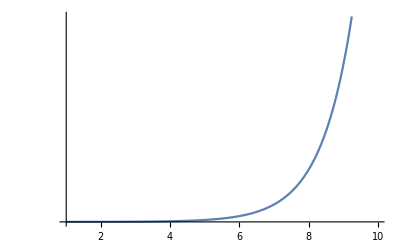

```mathematica
LogPlot[1+4^3^(-1+n)+16^3^(-1+n),{n,1,10}]
```